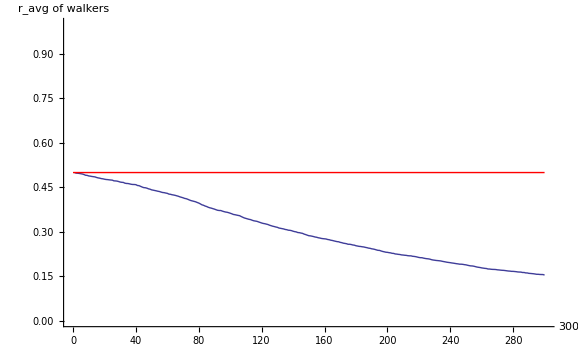

```mathematica
allwalks=Table[Subscript[datawalker, i],{i,1,num}];
norms=Map[Norm,allwalks,{2}];
all=Flatten[Table[norms[[p]],{p,1,num}]];
ravg=ListPlot[Table[Mean[Table[norms[[k,j]],{k,1,num,1}]],{j,1,steps,1}],Joined->True,PlotRange->{{0,steps},{0,1}},AxesLabel->{steps,"r_avg of walkers"}];
Show[ravg,Plot[rad,{t,0,steps},PlotStyle->Red]]
```

```mathematica
allwalks=Table[Subscript[datawalker, i],{i,1,num}];
allwalknorms=Map[Norm,allwalks,{2}];
ListAnimate[Table[Histogram[Table[allwalknorms[[w,t]],{w,1,num}],25,PlotRange->{{0,1},{0,num}},Frame-> True,Axes->False],{t,1,steps}]]
```